# BayesWave Prior

```mathematica
(* Unnormalized *)

ptilde[r_, dstar]:=r^2/(2r/(3dstar)+1)^5
```

## Normalization

```mathematica
Integrate[ptilde[r,dstar],{r,dmin,dmax},Assumptions->{dmin>0,dstar>dmin,dmax>dstar}]
```

(243 (dmax-dmin) dstar^5 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))/(2 (2 dmax+3 dstar)^4 (2 dmin+3 dstar)^4)

```mathematica
%//FortranForm
```

(243*(dmax - dmin)*dstar**5*
     -    (8*dmax**2*dmin**2*(dmax + dmin) + 
     -      8*dmax*dmin*(dmax**2 + 7*dmax*dmin + dmin**2)*dstar + 
     -      3*(dmax + dmin)*(dmax**2 + 16*dmax*dmin + dmin**2)*dstar**2 + 
     -      18*(dmax**2 + dmax*dmin + dmin**2)*dstar**3))/
     -  (2.*(2*dmax + 3*dstar)**4*(2*dmin + 3*dstar)**4)

## CDF

```mathematica
Integrate[ptilde[r,dstar],{r,dmin,d},Assumptions->{dmin>0,dstar>dmin,dmax>dstar}]
```

```mathematica
Integrate[27dstar^2r^2/(2r/(3dstar)+1)^5,{r,dmin,dmax},Assumptions->{dmin>0,dstar>dmin,dmax>dstar}]
```

```mathematica
norm = Integrate[27dstar^2r^2/(2r/(3dstar)+1)^5,{r,dmin,dmax},Assumptions->{dmin>0,dstar>dmin,dmax>dstar}]
```

(6561 (dmax-dmin) dstar^7 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))/(2 (2 dmax+3 dstar)^4 (2 dmin+3 dstar)^4)

```mathematica
FullSimplify[%112,{dmin>0,dstar>dmin,dmax>dstar}]
```

(243 (dmax-dmin) dstar^5 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))/(2 (2 dmax+3 dstar)^4 (2 dmin+3 dstar)^4)

```mathematica
p[r_]:=27 r^2 dstar^2/(2r/(3dstar)+1)^5/norm
```

```mathematica
p[r]//Simplify
```

(2 (2 dmax+3 dstar)^4 (2 dmin+3 dstar)^4 r^2)/(243 (dmax-dmin) (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3) (dstar+(2 r)/3)^5)

```mathematica
p[x]//FortranForm
```

(2*(2*dmax + 3*dstar)**4*(2*dmin + 3*dstar)**4*x**2)/
     -  (243.*(dmax - dmin)*dstar**5*
     -    (8*dmax**2*dmin**2*(dmax + dmin) + 
     -      8*dmax*dmin*(dmax**2 + 7*dmax*dmin + dmin**2)*dstar + 
     -      3*(dmax + dmin)*(dmax**2 + 16*dmax*dmin + dmin**2)*dstar**2 + 
     -      18*(dmax**2 + dmax*dmin + dmin**2)*dstar**3)*(1 + (2*x)/(3.*dstar))**5)

```mathematica
cdf/.d->x//FortranForm
```

((2*dmax + 3*dstar)**4*(-dmin + x)*
     -    (8*dmin**2*x**2*(dmin + x) + 18*dstar**3*(dmin**2 + dmin*x + x**2) + 
     -      8*dmin*dstar*x*(dmin**2 + 7*dmin*x + x**2) + 
     -      3*dstar**2*(dmin + x)*(dmin**2 + 16*dmin*x + x**2)))/
     -  ((dmax - dmin)*(8*dmax**2*dmin**2*(dmax + dmin) + 
     -      8*dmax*dmin*(dmax**2 + 7*dmax*dmin + dmin**2)*dstar + 
     -      3*(dmax + dmin)*(dmax**2 + 16*dmax*dmin + dmin**2)*dstar**2 + 
     -      18*(dmax**2 + dmax*dmin + dmin**2)*dstar**3)*(3*dstar + 2*x)**4)

```mathematica
Integrate[p[r],{r,dmin,dmax}, Assumptions->{dmin>0,dstar>dmin,dmax>dstar}]
```

1

```mathematica
D[p[r],r]/.r->dstar
```

0

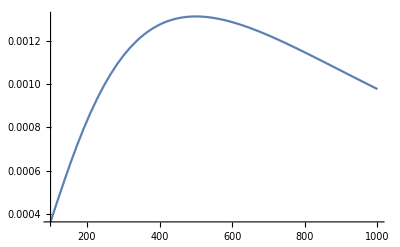

```mathematica
Plot[p[r]/.{dmin->100,dmax->1000,dstar->500},{r,100,1000}]
```

```mathematica
cdf = Integrate[p[r],{r,dmin,d},Assumptions->{dstar>dmin, dmin>0, d>dmin,dstar>0}]
```

((d-dmin) (2 dmax+3 dstar)^4 (8 d^2 dmin^2 (d+dmin)+8 d dmin (d^2+7 d dmin+dmin^2) dstar+3 (d+dmin) (d^2+16 d dmin+dmin^2) dstar^2+18 (d^2+d dmin+dmin^2) dstar^3))/((dmax-dmin) (2 d+3 dstar)^4 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))

```mathematica
cdf
```

((d-dmin) (2 dmax+3 dstar)^4 (8 d^2 dmin^2 (d+dmin)+8 d dmin (d^2+7 d dmin+dmin^2) dstar+3 (d+dmin) (d^2+16 d dmin+dmin^2) dstar^2+18 (d^2+d dmin+dmin^2) dstar^3))/((dmax-dmin) (2 d+3 dstar)^4 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))

```mathematica
Simplify[16 ((d^3 (d+6 dstar))/(2 d+3 dstar)^4-(dmin^3 (dmin+6 dstar))/(2 dmin+3 dstar)^4)]
```

16 ((d^3 (d+6 dstar))/(2 d+3 dstar)^4-(dmin^3 (dmin+6 dstar))/(2 dmin+3 dstar)^4)

```mathematica
Solve[16 ((d^3 (d+6 dstar))/(2 d+3 dstar)^4-(dmin^3 (dmin+6 dstar))/(2 dmin+3 dstar)^4)==u,d,]
```

$Aborted

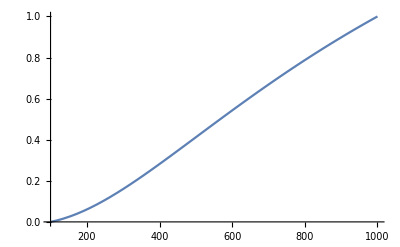

```mathematica
Plot[cdf/.{dmin->100,dmax->1000,dstar->500},{d,100,1000}]
```

```mathematica
cdf/.{dmin->100,dmax->1000,dstar->500,d->1000}
```

1

```mathematica
cdf
```

((d-dmin) (2 dmax+3 dstar)^4 (8 d^2 dmin^2 (d+dmin)+8 d dmin (d^2+7 d dmin+dmin^2) dstar+3 (d+dmin) (d^2+16 d dmin+dmin^2) dstar^2+18 (d^2+d dmin+dmin^2) dstar^3))/((dmax-dmin) (2 d+3 dstar)^4 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))

```mathematica
FullSimplify[cdf,{dmin>0,dstar>dmin,dmax>dstar, d>dmin, d<dmax}]
```

((d-dmin) (2 dmax+3 dstar)^4 (8 d^2 dmin^2 (d+dmin)+8 d dmin (d^2+7 d dmin+dmin^2) dstar+3 (d+dmin) (d^2+16 d dmin+dmin^2) dstar^2+18 (d^2+d dmin+dmin^2) dstar^3))/((dmax-dmin) (2 d+3 dstar)^4 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))

```mathematica
??Solve
```

```mathematica
cdf
```

((d-dmin) (2 dmax+3 dstar)^4 (8 d^2 dmin^2 (d+dmin)+8 d dmin (d^2+7 d dmin+dmin^2) dstar+3 (d+dmin) (d^2+16 d dmin+dmin^2) dstar^2+18 (d^2+d dmin+dmin^2) dstar^3))/((dmax-dmin) (2 d+3 dstar)^4 (8 dmax^2 dmin^2 (dmax+dmin)+8 dmax dmin (dmax^2+7 dmax dmin+dmin^2) dstar+3 (dmax+dmin) (dmax^2+16 dmax dmin+dmin^2) dstar^2+18 (dmax^2+dmax dmin+dmin^2) dstar^3))

```mathematica
Solve[cdf==u &&u∈Interval[{0,1}]&&dstar>dmin &&dmin>0&&dmax>dmin&&d>dmin &&dmax>d,d]
```

{{d→ConditionalExpression[Root[48 dmax^4 dmin^4 dstar^2+288 dmax^4 dmin^3 dstar^3+288 dmax^3 dmin^4 dstar^3+1728 dmax^3 dmin^3 dstar^4+648 dmax^2 dmin^4 dstar^4+3888 dmax^2 dmin^3 dstar^5+648 dmax dmin^4 dstar^5+3888 dmax dmin^3 dstar^6+243 dmin^4 dstar^6+1458 dmin^3 dstar^7+648 dmax^4 dmin^2 dstar^4 u1-648 dmax^2 dmin^4 dstar^4 u1+648 dmax^4 dmin dstar^5 u1+3888 dmax^3 dmin^2 dstar^5 u1-3888 dmax^2 dmin^3 dstar^5 u1-648 dmax dmin^4 dstar^5 u1+243 dmax^4 dstar^6 u1+3888 dmax^3 dmin dstar^6 u1-3888 dmax dmin^3 dstar^6 u1-243 dmin^4 dstar^6 u1+1458 dmax^3 dstar^7 u1-1458 dmin^3 dstar^7 u1+(128 dmax^4 dmin^4 dstar+768 dmax^4 dmin^3 dstar^2+768 dmax^3 dmin^4 dstar^2+4608 dmax^3 dmin^3 dstar^3+1728 dmax^2 dmin^4 dstar^3+10368 dmax^2 dmin^3 dstar^4+1728 dmax dmin^4 dstar^4+10368 dmax dmin^3 dstar^5+648 dmin^4 dstar^5+3888 dmin^3 dstar^6+1728 dmax^4 dmin^2 dstar^3 u1-1728 dmax^2 dmin^4 dstar^3 u1+1728 dmax^4 dmin dstar^4 u1+10368 dmax^3 dmin^2 dstar^4 u1-10368 dmax^2 dmin^3 dstar^4 u1-1728 dmax dmin^4 dstar^4 u1+648 dmax^4 dstar^5 u1+10368 dmax^3 dmin dstar^5 u1-10368 dmax dmin^3 dstar^5 u1-648 dmin^4 dstar^5 u1+3888 dmax^3 dstar^6 u1-3888 dmin^3 dstar^6 u1) #1+(128 dmax^4 dmin^4+768 dmax^4 dmin^3 dstar+768 dmax^3 dmin^4 dstar+4608 dmax^3 dmin^3 dstar^2+1728 dmax^2 dmin^4 dstar^2+10368 dmax^2 dmin^3 dstar^3+1728 dmax dmin^4 dstar^3+10368 dmax dmin^3 dstar^4+648 dmin^4 dstar^4+3888 dmin^3 dstar^5+1728 dmax^4 dmin^2 dstar^2 u1-1728 dmax^2 dmin^4 dstar^2 u1+1728 dmax^4 dmin dstar^3 u1+10368 dmax^3 dmin^2 dstar^3 u1-10368 dmax^2 dmin^3 dstar^3 u1-1728 dmax dmin^4 dstar^3 u1+648 dmax^4 dstar^4 u1+10368 dmax^3 dmin dstar^4 u1-10368 dmax dmin^3 dstar^4 u1-648 dmin^4 dstar^4 u1+3888 dmax^3 dstar^5 u1-3888 dmin^3 dstar^5 u1) #1^2+(-768 dmax^4 dmin^2 dstar-768 dmax^4 dmin dstar^2-4608 dmax^3 dmin^2 dstar^2-288 dmax^4 dstar^3-4608 dmax^3 dmin dstar^3-10368 dmax^2 dmin^2 dstar^3-1728 dmax^3 dstar^4-10368 dmax^2 dmin dstar^4-10368 dmax dmin^2 dstar^4-3888 dmax^2 dstar^5-10368 dmax dmin dstar^5-3888 dmin^2 dstar^5-3888 dmax dstar^6-3888 dmin dstar^6-1458 dstar^7+768 dmax^4 dmin^2 dstar u1-768 dmax^2 dmin^4 dstar u1+768 dmax^4 dmin dstar^2 u1+4608 dmax^3 dmin^2 dstar^2 u1-4608 dmax^2 dmin^3 dstar^2 u1-768 dmax dmin^4 dstar^2 u1+288 dmax^4 dstar^3 u1+4608 dmax^3 dmin dstar^3 u1-4608 dmax dmin^3 dstar^3 u1-288 dmin^4 dstar^3 u1+1728 dmax^3 dstar^4 u1-1728 dmin^3 dstar^4 u1) #1^3+(-128 dmax^4 dmin^2-128 dmax^4 dmin dstar-768 dmax^3 dmin^2 dstar-48 dmax^4 dstar^2-768 dmax^3 dmin dstar^2-1728 dmax^2 dmin^2 dstar^2-288 dmax^3 dstar^3-1728 dmax^2 dmin dstar^3-1728 dmax dmin^2 dstar^3-648 dmax^2 dstar^4-1728 dmax dmin dstar^4-648 dmin^2 dstar^4-648 dmax dstar^5-648 dmin dstar^5-243 dstar^6+128 dmax^4 dmin^2 u1-128 dmax^2 dmin^4 u1+128 dmax^4 dmin dstar u1+768 dmax^3 dmin^2 dstar u1-768 dmax^2 dmin^3 dstar u1-128 dmax dmin^4 dstar u1+48 dmax^4 dstar^2 u1+768 dmax^3 dmin dstar^2 u1-768 dmax dmin^3 dstar^2 u1-48 dmin^4 dstar^2 u1+288 dmax^3 dstar^3 u1-288 dmin^3 dstar^3 u1) #1^4&,2],dstar>0&&0<dmin<dstar&&dmax>dmin&&0<u1<1]}}

```mathematica
?Interval
```

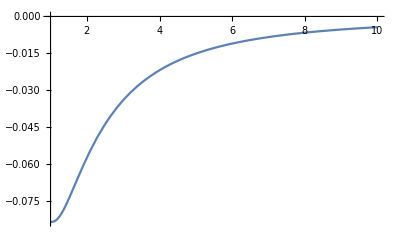

```mathematica
Plot[-1/(2y^2)+2/(3y^3)-1/(4y^4), {y,1,10}]
```

```mathematica
Solve[α^3+α^2/(2A)+α (1/(4A)-1)/(4A)-1/(18A^2)==0,α]
```

{{α→-1/(6 A)-(4 (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))+1/12 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)},{α→-1/(6 A)+(2 (1+ⅈ √3) (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))-1/24 (1-ⅈ √3) (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)},{α→-1/(6 A)+(2 (1-ⅈ √3) (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))-1/24 (1+ⅈ √3) (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)}}

```mathematica
FullSimplify[%159,{A<0}]
```

{{α→(1+(-1-12 A+2 √3 √-A Abs[1+12 A])^(2/3)-2 A (-6+((1+12 A+2 ⅈ √3 √A Abs[1+12 A])/A^3)^(1/3)))/(12 A^2 ((1+12 A+2 ⅈ √3 √A Abs[1+12 A])/A^3)^(1/3))},{α→1/24 (-4/A+((-1-ⅈ √3) (1+12 A))/(A^2 ((1+12 A+2 ⅈ √3 √A Abs[1+12 A])/A^3)^(1/3))+ⅈ (ⅈ+√3) ((1+12 A+2 ⅈ √3 √A Abs[1+12 A])/A^3)^(1/3))},{α→(-4+((1-ⅈ √3) (1+12 A))/(-1-12 A+2 √3 √-A Abs[1+12 A])^(1/3)+(1+ⅈ √3) (-1-12 A+2 √3 √-A Abs[1+12 A])^(1/3))/(24 A)}}

```mathematica
%159/.A->-1//N
```

{{α→0.221503},{α→0.139249+0.481063 ⅈ},{α→0.139249-0.481063 ⅈ}}

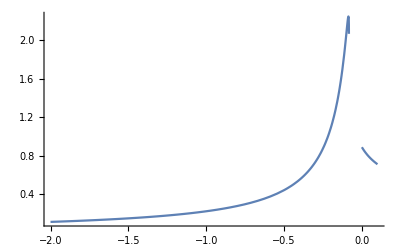

```mathematica
Plot[-1/(6 A)-(4 (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))+1/12 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3),{A,-2,.1},PlotRange->All]
```

Cubic

```mathematica
Discriminant[α^3+α^2/(2A)+α (1/(4A)-1)/(4A)-1/(18A^2),α]
```

(1+24 A+144 A^2)/(2304 A^5)

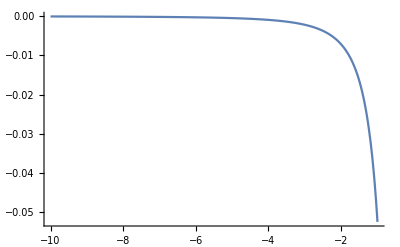

```mathematica
Plot[(1+24 A+144 A^2)/(2304 A^5),{A,-10,-1},PlotRange->All]
```

```mathematica
Solve[(1+24 A+144 A^2)/(2304 A^5)==0,A]
```

{{A→-1/12},{A→-1/12}}

```mathematica
Solve[α^3+α^2/(2A)+α (1/(4A)-1)/(4A)-1/(18A^2)==0,α]
```

{{α→-1/(6 A)-(4 (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))+1/12 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)},{α→-1/(6 A)+(2 (1+ⅈ √3) (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))-1/24 (1-ⅈ √3) (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)},{α→-1/(6 A)+(2 (1-ⅈ √3) (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))-1/24 (1+ⅈ √3) (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3)}}

```mathematica
%188/.A->-1/24//N
```

{{α→5.47569-0.730036 ⅈ},{α→1.04863+5.55112×10^-16 ⅈ},{α→5.47569+0.730036 ⅈ}}

```mathematica
FullSimplify[-1/(6 A)+(2 (1+ⅈ √3) (-1/(16 A^2)-3/(4 A)))/(3 (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3))-1/24 (1-ⅈ √3) (1/A^3+12/A^2+(2 √3 √(-1-24 A-144 A^2))/A^(5/2))^(1/3),{A>-1/12,A<0}]
```

-(-2+4 √3 √-A+A^2 (((-1+2 √3 √-A) (1+12 A))/A^3)^(2/3)+((1+12 A) (-1+4 √3 √-A+12 A)^2)^(1/3))/(12 (-1+2 √3 √-A) A)

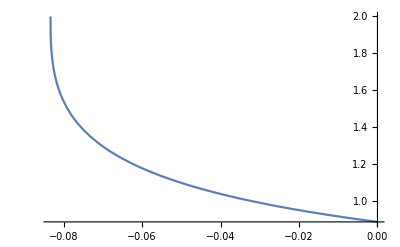

```mathematica
Plot[-(-2+4 √3 √-A+A^2 (((-1+2 √3 √-A) (1+12 A))/A^3)^(2/3)+((1+12 A) (-1+4 √3 √-A+12 A)^2)^(1/3))/(12 (-1+2 √3 √-A) A),{A,-1/12,0}]
```

```mathematica
α0=-(-2+4 √3 √-A+A^2 (((-1+2 √3 √-A) (1+12 A))/A^3)^(2/3)+((1+12 A) (-1+4 √3 √-A+12 A)^2)^(1/3))/(12 (-1+2 √3 √-A) A)
```

-(-2+4 √3 √-A+A^2 (((-1+2 √3 √-A) (1+12 A))/A^3)^(2/3)+((1+12 A) (-1+4 √3 √-A+12 A)^2)^(1/3))/(12 (-1+2 √3 √-A) A)

```mathematica
α0//FortranForm
```

-(-2 + 4*Sqrt(3)*Sqrt(-A) + 
     -     A**2*(((-1 + 2*Sqrt(3)*Sqrt(-A))*(1 + 12*A))/A**3)**0.6666666666666666 + 
     -     ((1 + 12*A)*(-1 + 4*Sqrt(3)*Sqrt(-A) + 12*A)**2)**0.3333333333333333)/
     -  (12.*(-1 + 2*Sqrt(3)*Sqrt(-A))*A)

```mathematica
Limit[α0,A->-1/12]
```

2

```mathematica
Limit[α0,A->0,Direction->"FromBelow"]
```

8/9

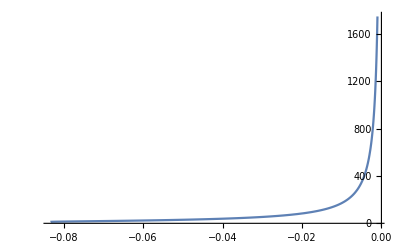

```mathematica
Plot[-1/A-2α0-2/(3α0 A),{A,-1/12,-0.001},PlotRange->{0,All}]
```

```mathematica
r1=-Sqrt[α0]/Sqrt[2]+1/2 Sqrt[-1/A-2α0-(2/(3A))Sqrt[2/α0]];
r2=-Sqrt[α0]/Sqrt[2]-1/2 Sqrt[-1/A-2α0-(2/(3A))Sqrt[2/α0]];
r3=Sqrt[α0]/Sqrt[2]+1/2 Sqrt[-1/A-2α0+(2/(3A))Sqrt[2/α0]];
r4=Sqrt[α0]/Sqrt[2]-1/2 Sqrt[-1/A-2α0+(2/(3A))Sqrt[2/α0]];
```

```mathematica
Plot[r4,{A,-1/12,-0.001},PlotRange->{All,All}]
```

-Graphics-

```mathematica
r1/.A->-0.04
```

2.38541

```mathematica
-1/(4 y^4)+2/(3 y^3)-1/(2 y^2)/.y->%20
```

-0.0464764

```mathematica
Integrate[(y-1)^2/y^5,y]
```

-1/(4 y^4)+2/(3 y^3)-1/(2 y^2)